# Of bulk and boundaries: Generalized transfer matrices for tight-binding models

## Hofstadter Butterfly-Bulk state

```mathematica
M = ({{2Cos[ky-2π/3], 1, 0}, {1, 2Cos[ky+2π/3], 1}, {0, 1, 2Cos[ky]}});
J = ({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});
{V,Ξ,W} = SingularValueDecomposition[J];
r = MatrixRank[Ξ];
V = V[[All,1;;r]];
W = W[[All,1;;r]];
Ξ=DiagonalMatrix[Diagonal[Ξ][[1;;r]]];
𝒢=Simplify@Inverse[ϵ IdentityMatrix[3]-M];
𝒢vv=Simplify[V†.𝒢.V];
𝒢vw=Simplify[W†.𝒢.V];
𝒢wv=Simplify[V†.𝒢.W];
𝒢ww=Simplify[W†.𝒢.W];
```

```mathematica
T=Simplify[Join[Simplify@Join[Inverse[Ξ].Inverse[𝒢vw],-Inverse[Ξ].Inverse[𝒢vw].𝒢ww.Ξ,2],Simplify@Join[𝒢vv.Inverse[𝒢vw],(𝒢wv-𝒢vv.Inverse[𝒢vw].𝒢ww).Ξ,2]]];
```

```mathematica
Δ=Tr[TrigExpand[FullSimplify[T]]];
```

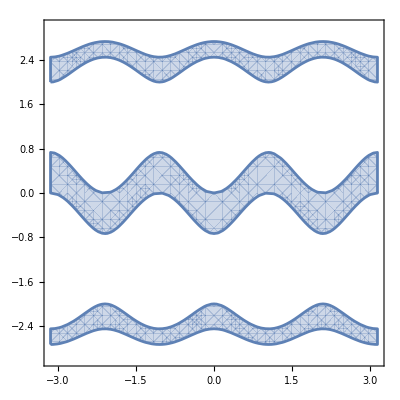

```mathematica
RegionPlot[Abs[Δ]<=2,{ky,-π,π},{ϵ,-3,3}]
```

Edge state

```mathematica
𝒥=({{0, 1}, {-1, 0}});Φ1=({{1}, {0}});ΦN=({{0}, {1}});
```

```mathematica
Show[ContourPlot[Simplify[First@Flatten[Transpose[Φ1].𝒥.T.Φ1,3]]==0,{ky,-π,π},{ϵ,-3,3},ColorFunction->Hue],RegionPlot[Abs[Δ]<=2,{ky,-π,π},{ϵ,-3,3}],ContourPlot[Simplify[First@Flatten[Transpose[ΦN].𝒥.T.ΦN,3]]==0,{ky,-π,π},{ϵ,-3,3},ColorFunction->(Blue&)]]
```

-Graphics-

```mathematica
First@Flatten[Transpose[Φ1].𝒥.T.Φ1,3]
```

-1+(ϵ-2 Cos[ky]) (ϵ+2 Sin[ky+π/6])

```mathematica
s = RandomReal[{-1,1},{5,5}]
```

{{-0.475841,-0.803936,-0.0354269,0.571072,-0.0793228},{-0.600684,-0.23987,0.970685,-0.348609,0.0981321},{-0.0343236,-0.162053,0.89222,0.549856,-0.515381},{0.879484,0.184181,0.904762,-0.647587,0.303727},{0.39789,-0.998626,-0.443135,-0.00730296,0.806836}}

```mathematica
{q,r}=QRDecomposition[s]
```

{{{-0.385928,-0.487182,-0.027838,0.713301,0.322707},{0.544798,0.0939251,0.119032,-0.00954424,0.82469},{-0.0475871,-0.605606,-0.555878,-0.539966,0.174394},{0.223962,-0.592062,0.73156,-0.169564,-0.188074},{-0.7084,0.191145,0.375334,-0.413274,0.387249}},{{1.23298,0.240746,0.0182994,-0.530145,0.474173},{0.,-1.30512,-0.19601,0.343985,0.567145},{0.,0.,-1.64795,0.226692,0.207539},{0.,0.,0.,0.847731,-0.656143},{0.,0.,0.,0.,0.068434}}}

```mathematica
q†.r
```

{{-0.475841,-0.803936,-0.0354269,0.571072,-0.0793228},{-0.600684,-0.23987,0.970685,-0.348609,0.0981321},{-0.0343236,-0.162053,0.89222,0.549856,-0.515381},{0.879484,0.184181,0.904762,-0.647587,0.303727},{0.39789,-0.998626,-0.443135,-0.00730296,0.806836}}

```mathematica
r.r//MatrixForm
```

(2.08442 | -0.231225 | -0.0519268 | -0.760545 | 0.0324495
-0.231225 | 2.18173 | 0.518699 | -0.0805222 | 0.038812
-0.0519268 | 0.518699 | 2.81021 | 0.0559984 | 0.0142027
-0.760545 | -0.0805222 | 0.0559984 | 1.14917 | -0.0449025
0.0324495 | 0.038812 | 0.0142027 | -0.0449025 | 0.00468321)

```mathematica
Power[r,2]//MatrixForm
```

(1.52023 | 0.0579585 | 0.000334868 | 0.281053 | 0.22484
0. | 1.70333 | 0.03842 | 0.118326 | 0.321654
0. | 0. | 2.71575 | 0.0513893 | 0.0430725
0. | 0. | 0. | 0.718648 | 0.430524
0. | 0. | 0. | 0. | 0.00468321)

```mathematica
Diagonal[r]^2
```

{1.52023,1.70333,2.71575,0.718648,0.00468321}